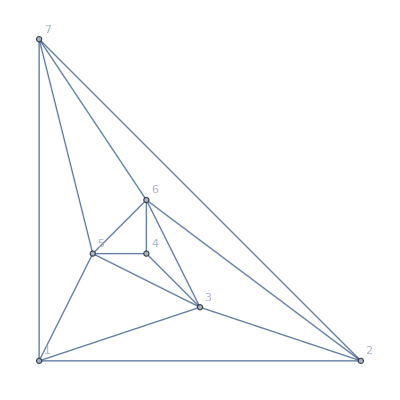

```mathematica
Graph[ReadGrof[6],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

```mathematica
CycleBaseCoeff[ChromaticPolynomial[ ReadGrof[50],x]]
```

{0,0,192,-176,-32,180,-148,59,-12,1}

```mathematica
CycleBaseCoeff[ChromaticPolynomial[ ReadGrof[50],x]].Inverse[FromNormalToCycle[10]]
```

{0,1458,-5103,7533,-6183,3105,-981,191,-21,1}

```mathematica
ChromaticPolynomial[ ReadGrof[50],x]
```

1458 x-5103 x^2+7533 x^3-6183 x^4+3105 x^5-981 x^6+191 x^7-21 x^8+x^9

```mathematica
MatrixForm[Rest[CycleBaseCoeff[ChromaticPolynomial[Rule2[ReadGrof[6],3<->5,1<->4],x]]].CycleBaseCoeff[ChromaticPolynomial[ ReadGrof[6],x]]]
```

5274

```mathematica
Rest[CycleBaseCoeff[ChromaticPolynomial[Rule2[ReadGrof[6],3<->5,1<->4],x]]].Rest[CycleBaseCoeff[ChromaticPolynomial[Rule2[ReadGrof[6],3<->5,1<->4],x]]]
```

37226

```mathematica
Rest[CycleBaseCoeff[ChromaticPolynomial[ ReadGrof[6],x]]].AdjacencyMatrix[ReadGrof[6]]
```

{29,13,1,14,0,30,-43}

```mathematica
CycleBaseCoeff[ChromaticPolynomial[ ReadGrof[6],x]].CycleBaseCoeff[ChromaticPolynomial[ ReadGrof[6],x]]
```

3188

```mathematica
Chrom[2]
```

24

```mathematica
Chrom[4]
```

96

```mathematica
deps2=ReadList["D:\\Grofs\\dependencies2.txt",Expression];Length[deps2]
```

1365053

```mathematica
Take[Sort[Tally[Map[{ CoefficientList[ChromaticPolynomial[ReadGrof[#[[1]]],x],x],#[[2]]}&,Select[Take[deps2,10000],Chrom[#[[1]]]>Chrom[#[[2]]]&]]],#1[[2]]>#2[[2]]&],100]
```

{{{{0,19278,-76167,131490,-131781,85474,-37688,11491,-2401,330,-27,1},3120},5},{{{0,19278,-76167,131490,-131781,85474,-37688,11491,-2401,330,-27,1},1835},4},{{{0,19278,-76167,131490,-131781,85474,-37688,11491,-2401,330,-27,1},2411},4},{{{0,19278,-76167,131490,-131781,85474,-37688,11491,-2401,330,-27,1},1998},4},{{{0,19278,-76167,131490,-131781,85474,-37688,11491,-2401,330,-27,1},1763},4},{{{0,-6426,23247,-36081,31900,-17858,6610,-1627,258,-24,1},754},4},{{{0,-6426,23247,-36081,31900,-17858,6610,-1627,258,-24,1},413},4},{{{0,-6426,23247,-36081,31900,-17858,6610,-1627,258,-24,1},591},4},{{{0,20682,-80973,138438,-137395,88273,-38576,11667,-2421,331,-27,1},4349},3},{{{0,19278,-76167,131490,-131781,85474,-37688,11491,-2401,330,-27,1},3440},3},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},1812},3},{{{0,19278,-76167,131490,-131781,85474,-37688,11491,-2401,330,-27,1},3142},3},{{{0,19278,-76167,131490,-131781,85474,-37688,11491,-2401,330,-27,1},3157},3},{{{0,19278,-76167,131490,-131781,85474,-37688,11491,-2401,330,-27,1},3007},3},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},2584},3},{{{0,19278,-76167,131490,-131781,85474,-37688,11491,-2401,330,-27,1},2416},3},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},1811},3},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},1729},3},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},1734},3},{{{0,-6426,23247,-36081,31900,-17858,6610,-1627,258,-24,1},770},3},{{{0,-5184,19386,-31185,28578,-16546,6307,-1589,256,-24,1},805},3},{{{0,-5184,19386,-31185,28578,-16546,6307,-1589,256,-24,1},523},3},{{{0,-5184,19386,-31185,28578,-16546,6307,-1589,256,-24,1},538},3},{{{0,-5184,19386,-31185,28578,-16546,6307,-1589,256,-24,1},391},3},{{{0,-5184,19386,-31185,28578,-16546,6307,-1589,256,-24,1},594},3},{{{0,-5184,19386,-31185,28578,-16546,6307,-1589,256,-24,1},597},3},{{{0,-6144,22400,-35062,31263,-17638,6570,-1624,258,-24,1},456},3},{{{0,-5184,19386,-31185,28578,-16546,6307,-1589,256,-24,1},431},3},{{{0,-6426,23247,-36081,31900,-17858,6610,-1627,258,-24,1},593},3},{{{0,-5184,19386,-31185,28578,-16546,6307,-1589,256,-24,1},389},3},{{{0,1728,-5886,8433,-6715,3277,-1010,193,-21,1},88},3},{{{0,-576,1770,-2221,1498,-593,139,-18,1},38},3},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},1974},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},1962},2},{{{0,23652,-90720,151767,-147432,92862,-39889,11898,-2444,332,-27,1},3416},2},{{{0,20682,-80973,138438,-137395,88273,-38576,11667,-2421,331,-27,1},5565},2},{{{0,24138,-92259,153765,-148827,93432,-40026,11916,-2445,332,-27,1},3388},2},{{{0,17010,-68445,120474,-123102,81321,-36448,11265,-2378,329,-27,1},4917},2},{{{0,19278,-76167,131490,-131781,85474,-37688,11491,-2401,330,-27,1},3742},2},{{{0,19278,-76167,131490,-131781,85474,-37688,11491,-2401,330,-27,1},2309},2},{{{0,17010,-68445,120474,-123102,81321,-36448,11265,-2378,329,-27,1},5434},2},{{{0,19278,-76167,131490,-131781,85474,-37688,11491,-2401,330,-27,1},5394},2},{{{0,19278,-76167,131490,-131781,85474,-37688,11491,-2401,330,-27,1},2291},2},{{{0,21492,-83592,141921,-139891,89321,-38835,11702,-2423,331,-27,1},3766},2},{{{0,21492,-83592,141921,-139891,89321,-38835,11702,-2423,331,-27,1},3438},2},{{{0,19278,-76167,131490,-131781,85474,-37688,11491,-2401,330,-27,1},5317},2},{{{0,17010,-68445,120474,-123102,81321,-36448,11265,-2378,329,-27,1},4232},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},5276},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},5274},2},{{{0,20682,-80973,138438,-137395,88273,-38576,11667,-2421,331,-27,1},3323},2},{{{0,20682,-80973,138438,-137395,88273,-38576,11667,-2421,331,-27,1},3336},2},{{{0,19278,-76167,131490,-131781,85474,-37688,11491,-2401,330,-27,1},5189},2},{{{0,20682,-80973,138438,-137395,88273,-38576,11667,-2421,331,-27,1},3308},2},{{{0,20682,-80973,138438,-137395,88273,-38576,11667,-2421,331,-27,1},3139},2},{{{0,19278,-76167,131490,-131781,85474,-37688,11491,-2401,330,-27,1},4747},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},3736},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},4387},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},4386},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},4497},2},{{{0,17010,-68445,120474,-123102,81321,-36448,11265,-2378,329,-27,1},4497},2},{{{0,24930,-94785,157084,-151188,94423,-40273,11950,-2447,332,-27,1},3835},2},{{{0,17928,-71712,125424,-127321,83550,-37199,11423,-2397,330,-27,1},2863},2},{{{0,17928,-71712,125424,-127321,83550,-37199,11423,-2397,330,-27,1},3830},2},{{{0,17928,-71712,125424,-127321,83550,-37199,11423,-2397,330,-27,1},4256},2},{{{0,17928,-71712,125424,-127321,83550,-37199,11423,-2397,330,-27,1},4268},2},{{{0,17928,-71712,125424,-127321,83550,-37199,11423,-2397,330,-27,1},3829},2},{{{0,17928,-71712,125424,-127321,83550,-37199,11423,-2397,330,-27,1},3485},2},{{{0,17928,-71712,125424,-127321,83550,-37199,11423,-2397,330,-27,1},2824},2},{{{0,19278,-76167,131490,-131781,85474,-37688,11491,-2401,330,-27,1},3002},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},4232},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},2350},2},{{{0,23652,-90720,151767,-147432,92862,-39889,11898,-2444,332,-27,1},4043},2},{{{0,23652,-90720,151767,-147432,92862,-39889,11898,-2444,332,-27,1},3408},2},{{{0,23652,-90720,151767,-147432,92862,-39889,11898,-2444,332,-27,1},3093},2},{{{0,19278,-76167,131490,-131781,85474,-37688,11491,-2401,330,-27,1},3441},2},{{{0,19278,-76167,131490,-131781,85474,-37688,11491,-2401,330,-27,1},4042},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},3222},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},2385},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},2199},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},4058},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},2412},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},4046},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},2158},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},3433},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},3427},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},2719},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},4033},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},2178},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},2216},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},2723},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},2232},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},4032},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},2076},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},4031},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},2117},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},3132},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},4030},2},{{{0,15552,-63342,112941,-116919,78216,-35467,11074,-2357,328,-27,1},2136},2},{{{0,18432,-73344,127586,-128851,84177,-37348,11442,-2398,330,-27,1},1685},2},{{{0,18432,-73344,127586,-128851,84177,-37348,11442,-2398,330,-27,1},3974},2}}

```mathematica
Map[#[[1]]&,Select[deps2,#[[2]]==87573&]]
```

{10615,10617,10767,11481,14767,14789,23134,23212,29299,29679}

```mathematica
VertexCount[ReadGrof[10615]]
```

13

```mathematica
Monitor[Table[
{CycleBaseCoeff[ChromaticPolynomial[ ReadGrof[g],x]],

MatrixForm[
Flatten[
Matt[14]/.Solve[

x2m1==1&&
x3m1==1&&x3m2==1&& 
x4m1==1&&x4m2==1&& x4m3==1&&
x5m1==1&&x5m2==1&& x5m3==1&& x5m4==1&&
x6m1==1&&x6m2==1&& x6m3==1&& x6m4==1&& x6m5==1&&
x7m1==1&&x7m2==1&& x7m3==1&& x7m4==1&& x7m5==1&& x7m6==1&&
x8m1==1&&x8m2==1&& x8m3==1&& x8m4==1&& x8m5==1&& x8m6==1&& x8m7==1&&
x9m1==1&&x9m2==1&& x9m3==1&& x9m4==1&& x9m5==1&& x9m6==1&& x9m7==1&&x9m8==1&&
x10m1==1&&x10m2==1&& x10m3==1&& x10m4==1&& x10m5==1&& x10m6==1&& x10m7==1&&x10m8==1&&x10m9==1&&
x11m1==1&&x11m2==1&& x11m3==1&& x11m4==1&& x11m5==1&& x11m6==1&& x11m7==1&&x11m8==1&&x11m9==1&&x11m10==1&&
x12m1==1&&x12m2==1&& x12m3==1&& x12m4==1&& x12m5==1&& x12m6==1&& x12m7==1&&x12m8==1&&x12m9==1&&x12m10==1&&x12m11==1&&
x13m1==1&&x13m2==1&& x13m3==1&& x13m4==1&& x13m5==1&& x13m6==1&& x13m7==1&&x13m8==1&&x13m9==1&&x13m10==1&&x13m11==1&&x13m12==1&&
SkewConst[14]&&
DiagConstr[14]&&
Problem[CoefficientList[ChromaticPolynomial[ ReadGrof[g],x],x],Rest[CoefficientList[ChromaticPolynomial[ReadGrof[87573],x],x]]]
,
Vars[14]
],1]
]
},{g,{10615,10617,10767,11481,14767,14789,23134,23212,29299,29679}}],g]
```

{{{0,0,14204,-23102,15389,4608,-18262,17771,-10259,3968,-1052,186,-20,1},(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
-764693 | 3621052 | -7533287 | 9238797 | -7509325 | 4290109 | -1775396 | 538390 | -119126 | 18809 | -2015 | 133 | -3 | 1)},{{0,0,12364,-20822,14765,3169,-16295,16518,-9778,3853,-1036,185,-20,1},(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
-764693 | 3621052 | -7552565 | 9295686 | -7583926 | 4347289 | -1803690 | 547784 | -121223 | 19113 | -2041 | 134 | -3 | 1)},{{0,0,12364,-20822,14765,3169,-16295,16518,-9778,3853,-1036,185,-20,1},(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
-764693 | 3621052 | -7552565 | 9295686 | -7583926 | 4347289 | -1803690 | 547784 | -121223 | 19113 | -2041 | 134 | -3 | 1)},{{0,0,12364,-20822,14765,3169,-16295,16518,-9778,3853,-1036,185,-20,1},(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
-764693 | 3621052 | -7552565 | 9295686 | -7583926 | 4347289 | -1803690 | 547784 | -121223 | 19113 | -2041 | 134 | -3 | 1)},{{0,0,14204,-23102,15389,4608,-18262,17771,-10259,3968,-1052,186,-20,1},(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
-764693 | 3621052 | -7533287 | 9238797 | -7509325 | 4290109 | -1775396 | 538390 | -119126 | 18809 | -2015 | 133 | -3 | 1)},{{0,0,14204,-23102,15389,4608,-18262,17771,-10259,3968,-1052,186,-20,1},(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
-764693 | 3621052 | -7533287 | 9238797 | -7509325 | 4290109 | -1775396 | 538390 | -119126 | 18809 | -2015 | 133 | -3 | 1)},{{0,0,14204,-23102,15389,4608,-18262,17771,-10259,3968,-1052,186,-20,1},(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
-764693 | 3621052 | -7533287 | 9238797 | -7509325 | 4290109 | -1775396 | 538390 | -119126 | 18809 | -2015 | 133 | -3 | 1)},{{0,0,12364,-20822,14765,3169,-16295,16518,-9778,3853,-1036,185,-20,1},(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
-764693 | 3621052 | -7552565 | 9295686 | -7583926 | 4347289 | -1803690 | 547784 | -121223 | 19113 | -2041 | 134 | -3 | 1)},{{0,0,12364,-20822,14765,3169,-16295,16518,-9778,3853,-1036,185,-20,1},(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
-764693 | 3621052 | -7552565 | 9295686 | -7583926 | 4347289 | -1803690 | 547784 | -121223 | 19113 | -2041 | 134 | -3 | 1)},{{0,0,12364,-20822,14765,3169,-16295,16518,-9778,3853,-1036,185,-20,1},(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
-764693 | 3621052 | -7552565 | 9295686 | -7583926 | 4347289 | -1803690 | 547784 | -121223 | 19113 | -2041 | 134 | -3 | 1)}}

```mathematica
Fold[And,
Map[
Problem[CycleBaseCoeff[ChromaticPolynomial[ ReadGrof[#[[1]]],x]],Rest[CycleBaseCoeff[ChromaticPolynomial[ReadGrof[#[[2]]],x]]]]&,
Select[Take[deps2,100],Chrom[#[[1]]]>Chrom[#[[2]]]&]
]
]
```

{39 x3m1-4 x4m1-31 x5m1+25 x6m1-8 x7m1+x8m1,39 x3m2-4 x4m2-31 x5m2+25 x6m2-8 x7m2+x8m2,39 x3m3-4 x4m3-31 x5m3+25 x6m3-8 x7m3+x8m3,39 x3m4-4 x4m4-31 x5m4+25 x6m4-8 x7m4+x8m4,39 x3m5-4 x4m5-31 x5m5+25 x6m5-8 x7m5+x8m5,39 x3m6-4 x4m6-31 x5m6+25 x6m6-8 x7m6+x8m6,39 x3m7-4 x4m7-31 x5m7+25 x6m7-8 x7m7+x8m7,39 x3m8-4 x4m8-31 x5m8+25 x6m8-8 x7m8+x8m8}=={0,-131,39,87,-95,43,-10,1}&&{43 x3m1-x4m1-35 x5m1+26 x6m1-8 x7m1+x8m1,43 x3m2-x4m2-35 x5m2+26 x6m2-8 x7m2+x8m2,43 x3m3-x4m3-35 x5m3+26 x6m3-8 x7m3+x8m3,43 x3m4-x4m4-35 x5m4+26 x6m4-8 x7m4+x8m4,43 x3m5-x4m5-35 x5m5+26 x6m5-8 x7m5+x8m5,43 x3m6-x4m6-35 x5m6+26 x6m6-8 x7m6+x8m6,43 x3m7-x4m7-35 x5m7+26 x6m7-8 x7m7+x8m7,43 x3m8-x4m8-35 x5m8+26 x6m8-8 x7m8+x8m8}=={0,-131,39,87,-95,43,-10,1}&&{-112 x3m1+45 x4m1+69 x5m1-87 x6m1+42 x7m1-10 x8m1+x9m1,-112 x3m2+45 x4m2+69 x5m2-87 x6m2+42 x7m2-10 x8m2+x9m2,-112 x3m3+45 x4m3+69 x5m3-87 x6m3+42 x7m3-10 x8m3+x9m3,-112 x3m4+45 x4m4+69 x5m4-87 x6m4+42 x7m4-10 x8m4+x9m4,-112 x3m5+45 x4m5+69 x5m5-87 x6m5+42 x7m5-10 x8m5+x9m5,-112 x3m6+45 x4m6+69 x5m6-87 x6m6+42 x7m6-10 x8m6+x9m6,-112 x3m7+45 x4m7+69 x5m7-87 x6m7+42 x7m7-10 x8m7+x9m7,-112 x3m8+45 x4m8+69 x5m8-87 x6m8+42 x7m8-10 x8m8+x9m8,-112 x3m9+45 x4m9+69 x5m9-87 x6m9+42 x7m9-10 x8m9+x9m9}=={0,328,-209,-135,277,-181,63,-12,1}&&{-112 x3m1+45 x4m1+69 x5m1-87 x6m1+42 x7m1-10 x8m1+x9m1,-112 x3m2+45 x4m2+69 x5m2-87 x6m2+42 x7m2-10 x8m2+x9m2,-112 x3m3+45 x4m3+69 x5m3-87 x6m3+42 x7m3-10 x8m3+x9m3,-112 x3m4+45 x4m4+69 x5m4-87 x6m4+42 x7m4-10 x8m4+x9m4,-112 x3m5+45 x4m5+69 x5m5-87 x6m5+42 x7m5-10 x8m5+x9m5,-112 x3m6+45 x4m6+69 x5m6-87 x6m6+42 x7m6-10 x8m6+x9m6,-112 x3m7+45 x4m7+69 x5m7-87 x6m7+42 x7m7-10 x8m7+x9m7,-112 x3m8+45 x4m8+69 x5m8-87 x6m8+42 x7m8-10 x8m8+x9m8,-112 x3m9+45 x4m9+69 x5m9-87 x6m9+42 x7m9-10 x8m9+x9m9}=={0,328,-209,-135,277,-181,63,-12,1}&&{-100 x3m1+47 x4m1+58 x5m1-81 x6m1+41 x7m1-10 x8m1+x9m1,-100 x3m2+47 x4m2+58 x5m2-81 x6m2+41 x7m2-10 x8m2+x9m2,-100 x3m3+47 x4m3+58 x5m3-81 x6m3+41 x7m3-10 x8m3+x9m3,-100 x3m4+47 x4m4+58 x5m4-81 x6m4+41 x7m4-10 x8m4+x9m4,-100 x3m5+47 x4m5+58 x5m5-81 x6m5+41 x7m5-10 x8m5+x9m5,-100 x3m6+47 x4m6+58 x5m6-81 x6m6+41 x7m6-10 x8m6+x9m6,-100 x3m7+47 x4m7+58 x5m7-81 x6m7+41 x7m7-10 x8m7+x9m7,-100 x3m8+47 x4m8+58 x5m8-81 x6m8+41 x7m8-10 x8m8+x9m8,-100 x3m9+47 x4m9+58 x5m9-81 x6m9+41 x7m9-10 x8m9+x9m9}=={0,328,-209,-135,277,-181,63,-12,1}&&{-100 x3m1+47 x4m1+58 x5m1-81 x6m1+41 x7m1-10 x8m1+x9m1,-100 x3m2+47 x4m2+58 x5m2-81 x6m2+41 x7m2-10 x8m2+x9m2,-100 x3m3+47 x4m3+58 x5m3-81 x6m3+41 x7m3-10 x8m3+x9m3,-100 x3m4+47 x4m4+58 x5m4-81 x6m4+41 x7m4-10 x8m4+x9m4,-100 x3m5+47 x4m5+58 x5m5-81 x6m5+41 x7m5-10 x8m5+x9m5,-100 x3m6+47 x4m6+58 x5m6-81 x6m6+41 x7m6-10 x8m6+x9m6,-100 x3m7+47 x4m7+58 x5m7-81 x6m7+41 x7m7-10 x8m7+x9m7,-100 x3m8+47 x4m8+58 x5m8-81 x6m8+41 x7m8-10 x8m8+x9m8,-100 x3m9+47 x4m9+58 x5m9-81 x6m9+41 x7m9-10 x8m9+x9m9}=={0,328,-209,-135,277,-181,63,-12,1}&&{-100 x3m1+47 x4m1+58 x5m1-81 x6m1+41 x7m1-10 x8m1+x9m1,-100 x3m2+47 x4m2+58 x5m2-81 x6m2+41 x7m2-10 x8m2+x9m2,-100 x3m3+47 x4m3+58 x5m3-81 x6m3+41 x7m3-10 x8m3+x9m3,-100 x3m4+47 x4m4+58 x5m4-81 x6m4+41 x7m4-10 x8m4+x9m4,-100 x3m5+47 x4m5+58 x5m5-81 x6m5+41 x7m5-10 x8m5+x9m5,-100 x3m6+47 x4m6+58 x5m6-81 x6m6+41 x7m6-10 x8m6+x9m6,-100 x3m7+47 x4m7+58 x5m7-81 x6m7+41 x7m7-10 x8m7+x9m7,-100 x3m8+47 x4m8+58 x5m8-81 x6m8+41 x7m8-10 x8m8+x9m8,-100 x3m9+47 x4m9+58 x5m9-81 x6m9+41 x7m9-10 x8m9+x9m9}=={0,328,-209,-135,277,-181,63,-12,1}&&{-131 x3m1+39 x4m1+87 x5m1-95 x6m1+43 x7m1-10 x8m1+x9m1,-131 x3m2+39 x4m2+87 x5m2-95 x6m2+43 x7m2-10 x8m2+x9m2,-131 x3m3+39 x4m3+87 x5m3-95 x6m3+43 x7m3-10 x8m3+x9m3,-131 x3m4+39 x4m4+87 x5m4-95 x6m4+43 x7m4-10 x8m4+x9m4,-131 x3m5+39 x4m5+87 x5m5-95 x6m5+43 x7m5-10 x8m5+x9m5,-131 x3m6+39 x4m6+87 x5m6-95 x6m6+43 x7m6-10 x8m6+x9m6,-131 x3m7+39 x4m7+87 x5m7-95 x6m7+43 x7m7-10 x8m7+x9m7,-131 x3m8+39 x4m8+87 x5m8-95 x6m8+43 x7m8-10 x8m8+x9m8,-131 x3m9+39 x4m9+87 x5m9-95 x6m9+43 x7m9-10 x8m9+x9m9}=={0,411,-208,-206,325,-193,64,-12,1}&&{-100 x3m1+47 x4m1+58 x5m1-81 x6m1+41 x7m1-10 x8m1+x9m1,-100 x3m2+47 x4m2+58 x5m2-81 x6m2+41 x7m2-10 x8m2+x9m2,-100 x3m3+47 x4m3+58 x5m3-81 x6m3+41 x7m3-10 x8m3+x9m3,-100 x3m4+47 x4m4+58 x5m4-81 x6m4+41 x7m4-10 x8m4+x9m4,-100 x3m5+47 x4m5+58 x5m5-81 x6m5+41 x7m5-10 x8m5+x9m5,-100 x3m6+47 x4m6+58 x5m6-81 x6m6+41 x7m6-10 x8m6+x9m6,-100 x3m7+47 x4m7+58 x5m7-81 x6m7+41 x7m7-10 x8m7+x9m7,-100 x3m8+47 x4m8+58 x5m8-81 x6m8+41 x7m8-10 x8m8+x9m8,-100 x3m9+47 x4m9+58 x5m9-81 x6m9+41 x7m9-10 x8m9+x9m9}=={0,328,-209,-135,277,-181,63,-12,1}&&{-100 x3m1+47 x4m1+58 x5m1-81 x6m1+41 x7m1-10 x8m1+x9m1,-100 x3m2+47 x4m2+58 x5m2-81 x6m2+41 x7m2-10 x8m2+x9m2,-100 x3m3+47 x4m3+58 x5m3-81 x6m3+41 x7m3-10 x8m3+x9m3,-100 x3m4+47 x4m4+58 x5m4-81 x6m4+41 x7m4-10 x8m4+x9m4,-100 x3m5+47 x4m5+58 x5m5-81 x6m5+41 x7m5-10 x8m5+x9m5,-100 x3m6+47 x4m6+58 x5m6-81 x6m6+41 x7m6-10 x8m6+x9m6,-100 x3m7+47 x4m7+58 x5m7-81 x6m7+41 x7m7-10 x8m7+x9m7,-100 x3m8+47 x4m8+58 x5m8-81 x6m8+41 x7m8-10 x8m8+x9m8,-100 x3m9+47 x4m9+58 x5m9-81 x6m9+41 x7m9-10 x8m9+x9m9}=={0,328,-209,-135,277,-181,63,-12,1}

```mathematica
Length[CycleBaseCoeff[ChromaticPolynomial[ ReadGrof[457],x]]]
```

12

```mathematica
Select[Take[deps2,10000],#[[2]]==3835&]
```

{{457,3835,{2,5<->11,7<->8}},{489,3835,{2,6<->8,3<->4}},{589,3835,{2,3<->5,7<->11}},{603,3835,{2,5<->7,3<->11}},{629,3835,{2,8<->10,5<->11}}}

```mathematica
{{□}, {Table[
{CycleBaseCoeff[ChromaticPolynomial[ ReadGrof[g],x]],

MatrixForm[
Flatten[
Matt[12]/.Solve[

x2m1==1&&
x3m1==1&&x3m2==1&& 
x4m1==1&&x4m2==1&& x4m3==1&&
x5m1==1&&x5m2==1&& x5m3==1&& x5m4==1&&
x6m1==1&&x6m2==1&& x6m3==1&& x6m4==1&& x6m5==1&&
x7m1==1&&x7m2==1&& x7m3==1&& x7m4==1&& x7m5==1&& x7m6==1&&
x8m1==1&&x8m2==1&& x8m3==1&& x8m4==1&& x8m5==1&& x8m6==1&& x8m7==1&&
x9m1==1&&x9m2==1&& x9m3==1&& x9m4==1&& x9m5==1&& x9m6==1&& x9m7==1&&x9m8==1&&
x10m1==1&&x10m2==1&& x10m3==1&& x10m4==1&& x10m5==1&& x10m6==1&& x10m7==1&&x10m8==1&&x10m9==1&&
x11m1==1&&x11m2==1&& x11m3==1&& x11m4==1&& x11m5==1&& x11m6==1&& x11m7==1&&x11m8==1&&x11m9==1&&x11m10==1&&
SkewConst[12]&&
DiagConstr[12]&&
Problem[CycleBaseCoeff[ChromaticPolynomial[ ReadGrof[g],x]],Rest[CycleBaseCoeff[ChromaticPolynomial[ReadGrof[3835],x]]]]
,
Vars[12]
],1]
]
},{g,{457,489,589,603,629}}]}}
```

{{□},{{{{0,0,2360,-2665,457,1896,-2296,1375,-505,117,-16,1},(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
-723 | -8291 | 8842 | -1570 | -6276 | 7508 | -4395 | 1574 | -355 | 49 | -2 | 1)},{{0,0,2700,-2867,284,2193,-2459,1416,-509,117,-16,1},(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
-859 | -8427 | 8706 | -1366 | -6274 | 7337 | -4269 | 1537 | -351 | 49 | -2 | 1)},{{0,0,2164,-2522,515,1729,-2169,1324,-494,116,-16,1},(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
-647 | -8215 | 8918 | -1690 | -6253 | 7589 | -4481 | 1615 | -365 | 50 | -2 | 1)},{{0,0,2912,-2981,167,2373,-2552,1438,-511,117,-16,1},(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
-947 | -8515 | 8618 | -1242 | -6264 | 7230 | -4196 | 1517 | -349 | 49 | -2 | 1)},{{0,0,2700,-2867,284,2193,-2459,1416,-509,117,-16,1},(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
-859 | -8427 | 8706 | -1366 | -6274 | 7337 | -4269 | 1537 | -351 | 49 | -2 | 1)}}}}

```mathematica
Sort[Tally[Map[#[[2]]&,Select[Take[deps2,10000],Chrom[#[[1]]]>Chrom[#[[2]]]&]]],#1[[2]]>#2[[2]]&]
```

{{3835,5},{3120,5},{2584,5},{1811,5},{1729,5},{1734,5},{805,5},{538,5},{594,5},{597,5},{431,5},{391,5},{389,5},{88,5},{4497,4},{4232,4},{3834,4},{3438,4},{3766,4},{2977,4},{3222,4},{3188,4},{2970,4},{2676,4},{2662,4},{1835,4},{2411,4},{1998,4},{1763,4},{1812,4},{1739,4},{1733,4},{1653,4},{1614,4},{1351,4},{1345,4},{1344,4},{1348,4},{1318,4},{1321,4},{754,4},{596,4},{595,4},{836,4},{834,4},{523,4},{661,4},{456,4},{657,4},{489,4},{629,4},{620,4},{600,4},{601,4},{413,4},{591,4},{463,4},{220,4},{221,4},{113,4},{38,4},{3416,3},{2319,3},{4349,3},{5276,3},{5274,3},{4386,3},{4387,3},{2863,3},{2824,3},{4268,3},{4256,3},{3440,3},{4043,3},{3408,3},{3093,3},{4033,3},{4032,3},{4031,3},{4030,3},{3427,3},{4058,3},{3433,3},{4046,3},{3734,3},{3974,3},{3840,3},{3827,3},{3484,3},{3772,3},{3485,3},{3736,3},{3538,3},{3448,3},{3142,3},{3157,3},{2385,3},{3193,3},{2350,3},{3363,3},{3091,3},{2412,3},{3189,3},{2232,3},{3132,3},{3187,3},{2216,3},{2199,3},{3186,3},{2178,3},{2158,3},{2136,3},{3183,3},{2117,3},{2076,3},{3126,3},{3160,3},{3076,3},{1685,3},{2966,3},{3049,3},{1640,3},{3046,3},{3023,3},{1600,3},{3007,3},{2719,3},{2953,3},{2521,3},{2723,3},{2634,3},{2633,3},{2589,3},{2502,3},{2097,3},{2473,3},{2416,3},{1836,3},{1838,3},{1962,3},{1641,3},{1974,3},{1774,3},{1773,3},{1742,3},{1642,3},{1260,3},{1246,3},{1237,3},{1251,3},{1346,3},{1347,3},{1343,3},{1303,3},{1323,3},{1316,3},{1294,3},{883,3},{906,3},{873,3},{890,3},{770,3},{856,3},{1190,3},{1189,3},{500,3},{738,3},{458,3},{815,3},{605,3},{840,3},{839,3},{837,3},{838,3},{841,3},{835,3},{602,3},{599,3},{721,3},{598,3},{564,3},{720,3},{550,3},{719,3},{718,3},{727,3},{725,3},{708,3},{698,3},{411,3},{410,3},{408,3},{457,3},{511,3},{510,3},{593,3},{442,3},{378,3},{387,3},{346,3},{386,3},{188,3},{222,3},{187,3},{217,3},{123,3},{99,3},{36,3},{3153,2},{2054,2},{2098,2},{5375,2},{5432,2},{2369,2},{5565,2},{2331,2},{3388,2},{4917,2},{5346,2},{3742,2},{2309,2},{5434,2},{2417,2},{3988,2},{4355,2},{5394,2},{2291,2},{3432,2},{5317,2},{3428,2},{3323,2},{3336,2},{5213,2},{5189,2},{3308,2},{5114,2},{5084,2},{4905,2},{2077,2},{4767,2},{3139,2},{4747,2},{4602,2},{4041,2},{4039,2},{4038,2},{4040,2},{4503,2},{4484,2},{4467,2},{4369,2},{4368,2},{3928,2},{3989,2},{2853,2},{3830,2},{2973,2},{2838,2},{2875,2},{3829,2},{2974,2},{2774,2},{3577,2},{3002,2},{4242,2},{3411,2},{3733,2},{4219,2},{2940,2},{2675,2},{3441,2},{4042,2},{3009,2},{2825,2},{2259,2},{4034,2},{3012,2},{3008,2},{2777,2},{2796,2},{2810,2},{1643,2},{1634,2},{2494,2},{2557,2},{3343,2},{2459,2},{2308,2},{3718,2},{3466,2},{2463,2},{2630,2},{3419,2},{3194,2},{3065,2},{2893,2},{3209,2},{3371,2},{2942,2},{3096,2},{3174,2},{2246,2},{3150,2},{3185,2},{3184,2},{3119,2},{3159,2},{2554,2},{2605,2},{3013,2},{3074,2},{2274,2},{3047,2},{3021,2},{3020,2},{2740,2},{2659,2},{2604,2},{2737,2},{2956,2},{2288,2},{2914,2},{2900,2},{2520,2},{2889,2},{2657,2},{2258,2},{2632,2},{2534,2},{2531,2},{2490,2},{2504,2},{2000,2},{1999,2},{1804,2},{1997,2},{1761,2},{2371,2},{1995,2},{2354,2},{2351,2},{1676,2},{1706,2},{2320,2},{1675,2},{1632,2},{2299,2},{1795,2},{1973,2},{1940,2},{1772,2},{1694,2},{1635,2},{1605,2},{1655,2},{1244,2},{1256,2},{1352,2},{1281,2},{1259,2},{1223,2},{882,2},{1273,2},{891,2},{739,2},{1319,2},{1302,2},{1301,2},{1292,2},{783,2},{855,2},{1191,2},{1142,2},{1140,2},{1139,2},{1121,2},{1112,2},{844,2},{904,2},{1084,2},{895,2},{814,2},{604,2},{606,2},{636,2},{722,2},{792,2},{667,2},{793,2},{665,2},{664,2},{663,2},{662,2},{617,2},{347,2},{585,2},{477,2},{483,2},{381,2},{197,2},{196,2},{223,2},{215,2},{207,2},{205,2},{122,2},{108,2},{172,2},{159,2},{94,2},{18,2},{2418,1},{3361,1},{3431,1},{3353,1},{3339,1},{2421,1},{3338,1},{3292,1},{2157,1},{3273,1},{2137,1},{3430,1},{3426,1},{2991,1},{2334,1},{2941,1},{3366,1},{3377,1},{1992,1},{2327,1},{2266,1},{5513,1},{4491,1},{3351,1},{5567,1},{3987,1},{5566,1},{3986,1},{2975,1},{4351,1},{3985,1},{4637,1},{5418,1},{4209,1},{4636,1},{4752,1},{4210,1},{5528,1},{4635,1},{4211,1},{5527,1},{4634,1},{4212,1},{4633,1},{4213,1},{3977,1},{3978,1},{4207,1},{3360,1},{2972,1},{5436,1},{4354,1},{2316,1},{5470,1},{5435,1},{3415,1},{4251,1},{4626,1},{4625,1},{4624,1},{4254,1},{5413,1},{4623,1},{4255,1},{4622,1},{2208,1},{4028,1},{2323,1},{2702,1},{3168,1},{4631,1},{4359,1},{3195,1},{1931,1},{5459,1},{3370,1},{3224,1},{4348,1},{1830,1},{5452,1},{4357,1},{5449,1},{3393,1},{4493,1},{3992,1},{5393,1},{5380,1},{3443,1},{5379,1},{3444,1},{5378,1},{3293,1},{5392,1},{3275,1},{5391,1},{5377,1},{5364,1},{4206,1},{3140,1},{5365,1},{4781,1},{5358,1},{3983,1},{4347,1},{1877,1},{2581,1},{4583,1},{2069,1},{3325,1},{3324,1},{4314,1},{3946,1},{5259,1},{4555,1},{5256,1},{4145,1},{3414,1},{5231,1},{5226,1},{5223,1},{5222,1},{5214,1},{4557,1},{5196,1},{4149,1},{4559,1},{5204,1},{3326,1},{3310,1},{3309,1},{3954,1},{3413,1},{5115,1},{4567,1},{5111,1},{4131,1},{4303,1},{4346,1},{3410,1},{5085,1},{4569,1},{5071,1},{4158,1},{4135,1},{3311,1},{5064,1},{5062,1},{4106,1},{4753,1},{4545,1},{3259,1},{2118,1},{3258,1},{4093,1},{4922,1},{4544,1},{3260,1},{4756,1},{4121,1},{4802,1},{4532,1},{3242,1},{4288,1},{3240,1},{4769,1},{4530,1},{3961,1},{4289,1},{4340,1},{3244,1},{4744,1},{2720,1},{4280,1},{4639,1},{4495,1},{4494,1},{3409,1},{3888,1},{4267,1},{4485,1},{4385,1},{3929,1},{4266,1},{4470,1},{4469,1},{4384,1},{2835,1},{3576,1},{4468,1},{2674,1},{4326,1},{4325,1},{4324,1},{4322,1},{4318,1},{4317,1},{4316,1},{4275,1},{4272,1},{3831,1},{3695,1},{3686,1},{3777,1},{4274,1},{4273,1},{3832,1},{3706,1},{3776,1},{3671,1},{3773,1},{4271,1},{3828,1},{3656,1},{4258,1},{2698,1},{2553,1},{4044,1},{4229,1},{3094,1},{2368,1},{4009,1},{3288,1},{2736,1},{3238,1},{2522,1},{2926,1},{4037,1},{3191,1},{4036,1},{3192,1},{4035,1},{3190,1},{3003,1},{3771,1},{3856,1},{3979,1},{3890,1},{3067,1},{3070,1},{3973,1},{3853,1},{3180,1},{3559,1},{3730,1},{3598,1},{3041,1},{1602,1},{3040,1},{3537,1},{3595,1},{3764,1},{3744,1},{3594,1},{3729,1},{3554,1},{3593,1},{3043,1},{3724,1},{3552,1},{3417,1},{3177,1},{3138,1},{3211,1},{2922,1},{3382,1},{2976,1},{3071,1},{3090,1},{2967,1},{3069,1},{3134,1},{3223,1},{3151,1},{3133,1},{3221,1},{3149,1},{3131,1},{3220,1},{3130,1},{3219,1},{3148,1},{3129,1},{3218,1},{3128,1},{3217,1},{3135,1},{3147,1},{3216,1},{3146,1},{3127,1},{3215,1},{3145,1},{3162,1},{3102,1},{3101,1},{2583,1},{3100,1},{3099,1},{1972,1},{1633,1},{3073,1},{3051,1},{2489,1},{3025,1},{2658,1},{2995,1},{2721,1},{2552,1},{2930,1},{2487,1},{2915,1},{2717,1},{2913,1},{2652,1},{2525,1},{2716,1},{2493,1},{2536,1},{2533,1},{2530,1},{2529,1},{2460,1},{2496,1},{2465,1},{1969,1},{1965,1},{1712,1},{1798,1},{2301,1},{1960,1},{2298,1},{1687,1},{2281,1},{1959,1},{1674,1},{2262,1},{1693,1},{1689,1},{1594,1},{1291,1},{1320,1},{791,1},{842,1},{776,1},{1330,1},{1325,1},{567,1},{630,1},{1326,1},{1324,1},{556,1},{631,1},{1327,1},{632,1},{570,1},{1333,1},{526,1},{1332,1},{524,1},{1305,1},{592,1},{1304,1},{832,1},{375,1},{436,1},{1293,1},{800,1},{905,1},{553,1},{633,1},{659,1},{405,1},{634,1},{789,1},{824,1},{337,1},{388,1},{627,1},{588,1},{658,1},{485,1},{437,1},{218,1},{216,1},{208,1},{206,1},{91,1},{40,1},{46,1}}

```mathematica
VertexCount[ReadGrof[727]]
```

11

```mathematica
deps2=ReadList["D:\\Grofs\\dependencies2.txt",Expression,10000]
```

{{1,2,{2,1<->4,2<->3}},{2,3,{2,2<->4,3<->5}},{2,4,{2,2<->5,1<->4}},{3,5,{2,1<->5,2<->3}},{3,6,{2,2<->5,1<->6}},{3,7,{2,3<->5,1<->4}},{3,8,{2,2<->6,3<->5}},{4,7,{2,2<->4,3<->6}},{5,10,{2,3<->4,5<->6}},{5,11,{2,3<->5,4<->7}},{5,12,{2,4<->5,3<->6}},{5,13,{2,2<->6,3<->5}},9977,{654,5114,{2,5<->9,2<->10}},{654,2904,{2,5<->10,8<->9}},{654,1974,{2,9<->10,5<->11}},{654,2428,{2,4<->10,6<->8}},{654,3402,{2,6<->10,4<->11}},{654,2412,{2,8<->10,4<->5}},{654,5674,{2,6<->11,9<->10}},{654,5675,{2,9<->11,6<->10}},{654,5676,{2,10<->11,6<->9}},{655,5677,{2,1<->7,3<->11}},{655,3974,{2,3<->7,1<->5}}}
 |  |  |  |

```mathematica
Length[deps2]
```

100

```mathematica
CycleBaseCoeff[ChromaticPolynomial[ ReadGrof[50],x]]
```

{0,0,192,-176,-32,180,-148,59,-12,1}

```mathematica
Rule2[ReadGrof[50],5<->6,8<->2]
```

```mathematica
With[
{size=12},
MatrixForm[
Matt[size]/.Solve[

Fold[And,
Map[
Problem[Prepend[CycleBaseCoeff[ChromaticPolynomial[ ReadGrof[#[[1]]],x]],0],CycleBaseCoeff[ChromaticPolynomial[ReadGrof[#[[2]]],x]]]&,
Select[Take[deps2,120],Chrom[#[[1]]]>Chrom[#[[2]]]&]
]
]
,
Vars[size]
]
]
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

((x1m1
x1m2
x1m3
x1m4
x1m5
x1m6
x1m7
x1m8
x1m9
x1m10
x1m11
x1m12) | (x2m1
x2m2
x2m3
x2m4
x2m5
x2m6
x2m7
x2m8
x2m9
x2m10
x2m11
x2m12) | (x3m1
x3m2
x3m3
x3m4
x3m5
x3m6
x3m7
x3m8
x3m9
x3m10
x3m11
x3m12) | (x4m1
x4m2
x4m3
x4m4
x4m5
x4m6
x4m7
x4m8
x4m9
x4m10
x4m11
x4m12) | (0
0
280
0
-237
164
-43
4
0
x5m10
x5m11
x5m12) | (x4m1
x4m2
477+x4m3
-1+x4m4
-403+x4m5
280+x4m6
-74+x4m7
7+x4m8
x4m9
x4m10+(3 x5m10)/2
x6m11
x6m12) | (0
0
1068
-4
-901
628
-167
16
0
(13 x5m10)/4
x7m11
x7m12) | (x4m1
x4m2
1721+x4m3
-13+x4m4
-1447+x4m5
1016+x4m6
-274+x4m7
27+x4m8
x4m9
x4m10+5 x5m10
x8m11
x8m12) | (0
0
2844
4
-2405
1669
-440
39
1
x9m10
x9m11
x9m12) | (x4m1
x4m2
3889+x4m3
98+x4m4
-3326+x4m5
2231+x4m6
-561+x4m7
48+x4m8
-2+x4m9
1+x4m10-(303 x5m10)/4+10 x9m10
x10m11
x10m12) | (x11m1
x11m2
x11m3
x11m4
x11m5
x11m6
x11m7
x11m8
x11m9
x11m10
x11m11
x11m12) | (x12m1
x12m2
x12m3
x12m4
x12m5
x12m6
x12m7
x12m8
x12m9
x12m10
x12m11
x12m12))

```mathematica
MatrixForm[{0,-131-43 x3m2+x4m2+35 x5m2-26 x6m2+8 x7m2,39-43 x3m3+x4m3+35 x5m3-26 x6m3+8 x7m3,87+x4m4+35 x5m4-26 x6m4+8 x7m4,-95+35 x5m5-26 x6m5+8 x7m5,43-26 x6m6+8 x7m6,-10+8 x7m7,1}]
```

(0
-131-43 x3m2+x4m2+35 x5m2-26 x6m2+8 x7m2
39-43 x3m3+x4m3+35 x5m3-26 x6m3+8 x7m3
87+x4m4+35 x5m4-26 x6m4+8 x7m4
-95+35 x5m5-26 x6m5+8 x7m5
43-26 x6m6+8 x7m6
-10+8 x7m7
1)

```mathematica
CycleBaseCoeff[ChromaticPolynomial[ ReadGrof[15],x]]
```

{0,0,-100,47,58,-81,41,-10,1}

```mathematica
Table[
{CycleBaseCoeff[ChromaticPolynomial[ ReadGrof[g],x]],

MatrixForm[
Flatten[
Matt[9]/.Solve[

x2m1==1&&
x3m1==1&&x3m2==1&& 
x4m1==1&&x4m2==1&& x4m3==1&&
x5m1==1&&x5m2==1&& x5m3==1&& x5m4==1&&
x6m1==1&&x6m2==1&& x6m3==1&& x6m4==1&& x6m5==1&&
x7m1==1&&x7m2==1&& x7m3==1&& x7m4==1&& x7m5==1&& x7m6==1&&
x8m1==1&&x8m2==1&& x8m3==1&& x8m4==1&& x8m5==1&& x8m6==1&& x8m7==1&&
SkewConst[9]&&
DiagConstr[9]&&
Problem[CycleBaseCoeff[ChromaticPolynomial[ ReadGrof[g],x]],Rest[CycleBaseCoeff[ChromaticPolynomial[ReadGrof[38],x]]]]
,
Vars[9]
],1]
]
},{g,{11,14,15,20}}]
```

{{{0,0,-112,45,69,-87,42,-10,1},(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
53 | 381 | -156 | -194 | 263 | -126 | 31 | -2 | 1)},{{0,0,-100,47,58,-81,41,-10,1},(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
45 | 373 | -164 | -190 | 269 | -131 | 32 | -2 | 1)},{{0,0,-100,47,58,-81,41,-10,1},(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
45 | 373 | -164 | -190 | 269 | -131 | 32 | -2 | 1)},{{0,0,-100,47,58,-81,41,-10,1},(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
45 | 373 | -164 | -190 | 269 | -131 | 32 | -2 | 1)}}

```mathematica
CycleBaseCoeff[ChromaticPolynomial[ReadGrof[38],x]]
```

{0,0,328,-209,-135,277,-181,63,-12,1}

```mathematica
{{53,381,-156,-194,263,-126,31,-2,1}}-{{45,373,-164,-190,269,-131,32,-2,1}}
```

{{8,8,8,-4,-6,5,-1,0,0}}

```mathematica
({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 1, 1, 0, 0, 0, 0, 0}, {0, 1, 1, 1, 0, 0, 0, 0}, {0, 1, 1, 1, 1, 0, 0, 0}, {0, 1, 1, 1, 1, 1, 0, 0}, {0, 1, 1, 1, 1, 1, 1, 0}, {0, -152, 18, 105, -81, 26, -2, 1}})
```

```mathematica
CycleBaseCoeff[ChromaticPolynomial[ ReadGrof[6],x]]
```

{0,0,39,-4,-31,25,-8,1}

```mathematica
Rest[CycleBaseCoeff[ChromaticPolynomial[ReadGrof[18],x]]]
```

{0,-131,39,87,-95,43,-10,1}

```mathematica
MatrixForm[{0,-131-39 x3m2+4 x4m2+31 x5m2-25 x6m2+8 x7m2,39-39 x3m3+4 x4m3+31 x5m3-25 x6m3+8 x7m3,87+4 x4m4+31 x5m4-25 x6m4+8 x7m4,-95+31 x5m5-25 x6m5+8 x7m5,43-25 x6m6+8 x7m6,-10+8 x7m7,1}]
```

(0
-131-39 x3m2+4 x4m2+31 x5m2-25 x6m2+8 x7m2
39-39 x3m3+4 x4m3+31 x5m3-25 x6m3+8 x7m3
87+4 x4m4+31 x5m4-25 x6m4+8 x7m4
-95+31 x5m5-25 x6m5+8 x7m5
43-25 x6m6+8 x7m6
-10+8 x7m7
1)

```mathematica
TableForm[
Map[
With[
{g=ReadGrof[#[[1]]],h=ReadGrof[#[[2]]]},
{MatrixForm[
Total[Most[CycleBaseCoeff[ChromaticPolynomial[g,x]]].AdjacencyMatrix[g]]
],MatrixForm[
Total[Most[CycleBaseCoeff[ChromaticPolynomial[h,x]]].AdjacencyMatrix[h]]
]}
]&,
Select[Take[deps2,100],Chrom[#[[1]]]>Chrom[#[[2]]]&]
], TableDepth->1
]
```

{152,-407}
{142,-407}
{-322,899}
{-322,932}
{-322,899}
{-326,899}
{-326,932}
{-407,1110}
{-205,932}
{-154,899}